```mathematica
(*  Constants defns *)
g = 9.81; (* accel grav *)
ρ = 1.225; (*Density of air *)
R = .00125; (* 2.5 mm diameter *)
d = .00025; (* ~0.2mm avg thickness*)
m = .0000017;  (* ~2 mg *)
μ=.000018; (*dyn visc -- not in use*)
e=.5; (* induced drag efficiency -- for analytical drag*)

(*g = 9.81; (* Acceleration due to gravity *)
ρ = 1.225; (* Density of air *)
R = .053; (* 5 cm radius coaster *)
d = .0017; (* Thickness ~ estimated. *)
m = .0059;  (* 5.9 g *)
ω = 49; (* Rotation rate in rad/s *)
μ=.000018; (*dynamic viscosity of air -- not currently used*)
e=.8; (* induced drag efficiency -- ellipitcal wing = 1, rectangular = 0.7 -- choose intermediate -- not currently used (using experimental drag coefficient instead) *)
L = 1/2 m*R^2*ω; (* ang mom. thin disc rotating about axis of symmetry *) *)
```

```mathematica
(* Make solver a function *)

(* Initial Conds & SOlver --- Need to redefine/recalculate forces INSIDE the functuon so that the vaired launch conditions are included in the force expressions *)
solveEquations[xo_,yo_,zo_,vxo_,vyo_,vzo_,αo_,ϕo_,ω_] := Module[{soln,disp,flighttime,zdisp},
Check[ (* Check is essentially a try-catch block, prevents a single error from stopping the entire remaining simulations *)
(* Force defns*)
V[t] = √(x'[t]^2+y'[t]^2+z'[t]^2); (* Velocity magnitude *)
L = 1/2 m*R^2*ω;

(* Angular momentum components in lab frame *)
Lx[t]=L*(x'[t]/V[t] Sin[α[t]]+y'[t]/V[t] Cos[α[t]]Cos[ϕ[t]]+z'[t]/V[t] Cos[α[t]]Sin[ϕ[t]]);
Ly[t]=L*(y'[t]/V[t] x'[t]/(√(x'[t]^2+z'[t]^2))Sin[α[t]]-(√(x'[t]^2+z'[t]^2))/V[t] Cos[α[t]]Cos[ϕ[t]]+y'[t]/V[t] z'[t]/(√(x'[t]^2+z'[t]^2))Cos[α[t]]Sin[ϕ[t]]);
Lz[t]=L*(z'[t]/(√(x'[t]^2+z'[t]^2))Sin[α[t]]-x'[t]/(√(x'[t]^2+z'[t]^2))Cos[α[t]]Sin[ϕ[t]]);
(*Lift components in lab frame - defined using the above ang mom components*)
(* Lift as function of v and l components*)
FLx[t]=(((π^2 R^2 ρ)/2 Sin[2α[t]] (x'[t]^2+y'[t]^2+z'[t]^2) (Ly[t] x'[t] y'[t]+Lz[t] x'[t] z'[t]-Lx[t] (y'[t]^2+z'[t]^2)))/(√((x'[t]^2+y'[t]^2+z'[t]^2) (Lz[t]^2 (x'[t]^2+y'[t]^2)-2 Lx[t] Lz[t] x'[t] z'[t]-2 Ly[t] y'[t] (Lx[t] x'[t]+Lz[t] z'[t])+Ly[t]^2 (x'[t]^2+z'[t]^2)+Lx[t]^2 (y'[t]^2+z'[t]^2)))));
FLy[t]=-((π^2 R^2 ρ)/2 Sin[2α[t]]  (x'[t]^2+y'[t]^2+z'[t]^2) (-y'[t] (Lx[t] x'[t]+Lz[t] z'[t])+Ly[t] (x'[t]^2+z'[t]^2)))/(√((x'[t]^2+y'[t]^2+z'[t]^2) (Lz[t]^2 (x'[t]^2+y'[t]^2)-2 Lx[t] Lz[t] x'[t] z'[t]-2 Ly[t] y'[t] (Lx[t] x'[t]+Lz[t] z'[t])+Ly[t]^2 (x'[t]^2+z'[t]^2)+Lx[t]^2 (y'[t]^2+z'[t]^2))));
FLz[t]=-((π^2 R^2 ρ)/2 Sin[2α[t]] (Lz[t] (x'[t]^2+y'[t]^2)-(Lx[t] x'[t]+Ly[t] y'[t]) z'[t]) (x'[t]^2+y'[t]^2+z'[t]^2))/(√((x'[t]^2+y'[t]^2+z'[t]^2) (Lz[t]^2 (x'[t]^2+y'[t]^2)-2 Lx[t] Lz[t] x'[t] z'[t]-2 Ly[t] y'[t] (Lx[t] x'[t]+Lz[t] z'[t])+Ly[t]^2 (x'[t]^2+z'[t]^2)+Lx[t]^2 (y'[t]^2+z'[t]^2))));



(* Drag force componenss. Using the experimentally determined value of CD for Ruellia seeds *)
(* Experimental drag expression based on measured Cd for R ciliatiflora *)
Subscript[C, D] = 0.301; (*5% uncertainity interval: (.259, .343) *)
Dx[t] = -(((Subscript[C, D]+(π^2*Abs[Sin[α[t]]]^2)/e)*ρ)/2 V[t]*x'[t](π*R^2 Abs[Sin[α[t]]]+2d*R*Abs[Cos[α[t]]]));
Dy[t] = -(((Subscript[C, D]+(π^2*Abs[Sin[α[t]]]^2)/e)*ρ)/2 V[t]*y'[t](π*R^2 Abs[Sin[α[t]]]+2d*R*Abs[Cos[α[t]]]));
Dz[t] = -(((Subscript[C, D]+(π^2*Abs[Sin[α[t]]]^2)/e)*ρ)/2 V[t]*z'[t](π*R^2 Abs[Sin[α[t]]]+2d*R*Abs[Cos[α[t]]]));


(* Experimental magnus exrpression based on measured Cm for R ciliatiflora *)
Subscript[C, M]=0.0351;(*5% uncertainity interval: (.018, .052) *)
Mx[t] = -1/2 Subscript[C, M] ρ(d*2R)V[t](y'[t](Sin[α[t]]*z'[t]/(√(x'[t]^2+z'[t]^2))-Cos[α[t]]Sin[ϕ[t]]*x'[t]/(√(x'[t]^2+z'[t]^2)))-z'[t](Sin[α[t]]*y'[t]/V[t]-Cos[α[t]]Cos[ϕ[t]]*(√(x'[t]^2+z'[t]^2))/V[t]));
My[t] = -1/2 Subscript[C, M] ρ(d*2R)V[t](z'[t](Sin[α[t]]*x'[t]/V[t]+Cos[α[t]]Cos[ϕ[t]]*y'[t]/V[t]+Cos[α[t]]Sin[ϕ[t]]*z'[t]/V[t])-x'[t](Sin[α[t]]*z'[t]/(√(x'[t]^2+z'[t]^2))-Cos[α[t]]Sin[ϕ[t]]*x'[t]/(√(x'[t]^2+z'[t]^2))));
Mz[t] =-1/2 Subscript[C, M] ρ(d*2R)V[t](x'[t](Sin[α[t]]*y'[t]/V[t]-Cos[α[t]]Cos[ϕ[t]]*(√(x'[t]^2+z'[t]^2))/V[t])-y'[t](Sin[α[t]]*x'[t]/V[t]+Cos[α[t]]Cos[ϕ[t]]*y'[t]/V[t]+Cos[α[t]]Sin[ϕ[t]]*z'[t]/V[t]));
Subscript[eq, α] = α'[t] == (g *√(x'[t]^2+z'[t]^2))/V[t]^2 Cos[ϕ[t]]-(ρ*V[t]*π^2*R^2)/(2m)Sin[2α[t]];
Subscript[eq, ϕ] = ϕ'[t] == -(π^3*R^3 ρ*V[t]^2)/(16*L)Sin[2*α[t]];
Subscript[eq, x] = x''[t]==1/m(FLx[t]+Dx[t]+Mx[t]);
Subscript[eq, y] = y''[t]== 1/m(FLy[t]+Dy[t]+My[t])-g;
Subscript[eq, z] = z''[t] ==1/m(FLz[t]+Dz[t]+Mz[t]);
soln = NDSolve[{

(* 5 ODES *)
 Subscript[eq, α],Subscript[eq, ϕ], Subscript[eq, x], Subscript[eq, y],Subscript[eq, z], 
(* Initial conditions *)
ϕ[0]==ϕo,
α[0]==αo,
x[0]==xo,x'[0]==vxo,
y[0]==yo,y'[0]==vyo,
z[0]==zo,z'[0]==vzo},

{α,ϕ,x,y,z},{t,0,10}]  ;

(* get time disc hits ground, total displacement *)
flighttime = Part[FindRoot[0==y[t]/.soln,{t,.01,10}, Method->"Brent"],1] //Last;
disp=√(x[flighttime]^2+z[flighttime]^2)/.soln;
zdisp=z[flighttime]/.soln;
Return[{ϕo*(360/(2π)),αo*(360/(2π)),ArcTan[vyo/vxo]*(360/(2π)),ω,flighttime,Part[disp,1],Part[zdisp,1],-1}],
Print[{"Error:",ϕo*(360/(2π)),ArcTan[vyo/vxo]*(360/(2π)),ω}]; (* Error catching -- return the simulated conditions so you know where stuff is breaking *)
Return[{ϕo*(360/(2π)),αo*(360/(2π)),ArcTan[vyo/vxo]*(360/(2π)),ω,-1,-1,-1,-1}]]]
```

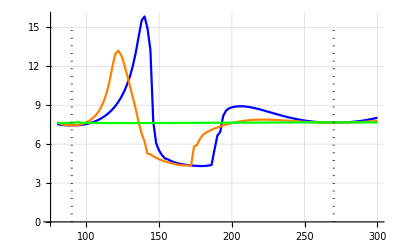

```mathematica
(*Initial betas 95% interval (38,42) *)
(*Phi ~270 (backspin), but not really possible to measure precisely *)
(*Initial velocities 95% interval (9.00, 10.63)*)
angles = Range[80*((2*π)/360),300*((2*π)/360),2*((2*π)/360)];
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[α, o]=(.1)*((2*π)/360);
Subscript[vx, o]=10*Cos[40*((2*π)/360)]; 
Subscript[vy, o]=10*Sin[40*((2*π)/360)];
Subscript[vz, o]=0; 

(* Quick check on dispersion range as function of phi for 3 different omegas. runs quickly & can be used to make sure everything is working properly.*)

(* General form for running a set of simulations using the Table command. Passes in each element of the list "angles" to the solver, solves the equations using the above initial conditions and the given phi value. *)
resultsTable = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[α, o],phi,3200*2π],{phi,angles}];
resultsTableMid = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[α, o],phi,1250*2π],{phi,angles}];
resultsTableLow = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[α, o],phi,20*2π],{phi,angles}];

(* For the vertical lines denoting top & backspin*)
topspin = Transpose@{{90,90},{0,15}};
backspin = Transpose@{{270,270},{0,15}};


datadisp = Transpose@{resultsTable[[All,1]],resultsTable[[All,6]]};
datadispMid = Transpose@{resultsTableMid[[All,1]],resultsTableMid[[All,6]]};
datadispLow = Transpose@{resultsTableLow[[All,1]],resultsTableLow[[All,6]]};

ListLinePlot[{datadisp,datadispMid,datadispLow, topspin,backspin},
PlotStyle->{{Blue},{Orange}, {Green},{Black,Dotted},{Black,Dotted}},
PlotRange->All, GridLines->Automatic]
```

```mathematica
angles = Range[90*((2*π)/360),270*((2*π)/360),10*((2*π)/360)];
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[α, o]=(.1)*((2*π)/360);
Subscript[vx, o]=10*Cos[40*((2*π)/360)]; 
Subscript[vy, o]=10*Sin[40*((2*π)/360)];
Subscript[vz, o]=0; 
ω=1250*2π;
resultsTablePhi = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[α, o],phi,ω],{phi,angles}];
```

{90,1.30276,7.45232,0.0285671}

{100,1.36709,7.67404,-1.55561}

{110,1.63598,8.81292,-3.68553}

{120,2.62836,12.9786,-6.50007}

{130,3.13337,10.4604,-2.87544}

{140,6.37721,6.20875,-1.6965}

{150,2.37298,4.83262,-1.35744}

{160,2.24662,4.48213,-0.531437}

{170,2.40185,4.35384,0.223823}

{180,2.50272,6.6983,3.4677}

{190,2.31274,7.28149,4.59086}

{200,2.12117,7.6249,4.83821}

{210,1.93594,7.82277,4.60585}

{220,1.76879,7.89083,4.04854}

{230,1.6283,7.86592,3.30897}

{240,1.51856,7.79364,2.49074}

{250,1.44084,7.71765,1.65298}

{260,1.39505,7.67219,0.81913}

{270,1.38075,7.67843,-0.0107439}

-Graphics3D-

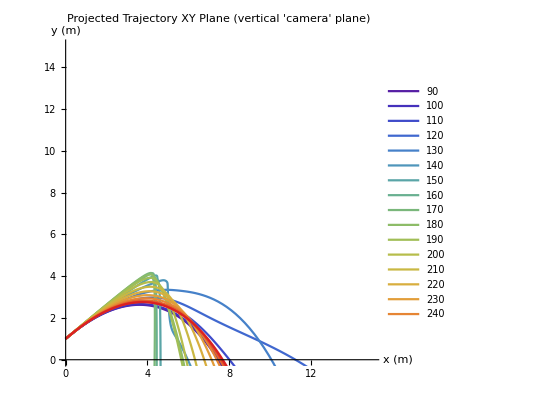

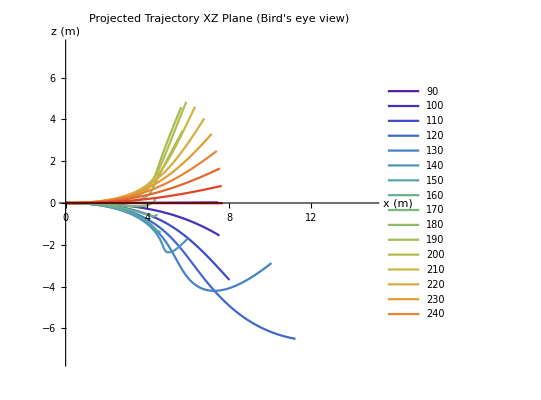

```mathematica
plotListXYZ = {};
plotListXY = {};
plotListXZ = {};
For[p=1, p<= Length[angles], p++,
Print[{resultsTablePhi[[p,1]],resultsTablePhi[[p,5]],resultsTablePhi[[p,6]],resultsTablePhi[[p,7]]}];
tland=resultsTablePhi[[p,5]];
soln=resultsTablePhi[[p,8]];
x[t]=soln{3};
y[t]=soln{4};
z[t]=soln{5};
plotXYZ = ParametricPlot3D[{x[t],y[t],z[t]}/.soln,{t,0,tland*1},
PlotRange->{{0,15},{0,5},{-7.5,7.5}}, 
PlotLabel->"3D trajectory ",
AxesLabel->{"x (m)","y (m)", "z (m)"},
PlotLegends->{resultsTablePhi[[p,1]]},
PlotStyle->{ColorData["Rainbow",p/Length[angles]]},
FaceGrids->{{1,0,0},{0,-1,0},{0,0,-1}},
ViewAngle->0.36449712460058503,ViewCenter->{0.5,0.5,0.5},
ViewMatrix->Automatic,ViewPoint->{-1.205461023704569,3.136085324249023,0.40228417736599875},
ViewProjection->Automatic,
ViewRange->All,
ViewVector->Automatic,
ViewVertical->{0.12734601200290835,0.9914635570294913,-0.027982285635446663}];

plotXY = ParametricPlot[{{x[t],y[t]}/.soln},{t,0,tland*1.1},
PlotRange->{{0,15},{0,15}}, 
PlotStyle->{ColorData["Rainbow",p/Length[angles]]},
PlotLabel->"Projected Trajectory XY Plane (vertical 'camera' plane) ",
AxesLabel->{"x (m)", "y (m)"},
PlotLegends->{resultsTablePhi[[p,1]]}];

plotXZ = ParametricPlot[{{x[t],z[t]}/.soln},{t,0,tland},
PlotRange->{{0,15},{-7.5,7.5}}, 
PlotStyle->{ColorData["Rainbow",p/Length[angles]]},
PlotLabel->"Projected Trajectory XZ Plane (Bird's eye view)",
AxesLabel->{"x (m)", "z (m)"},
PlotLegends->{resultsTablePhi[[p,1]]}];

AppendTo[plotListXYZ,plotXYZ];
AppendTo[plotListXY,plotXY];
AppendTo[plotListXZ,plotXZ];

]

XYZ=Show[plotListXYZ]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\seed\\sd_combinedXYZ.jpg",XYZ];
XY=Show[plotListXY]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\seed\\sd_combinedXY.jpg",XY];
XZ=Show[plotListXZ]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\seed\\sd_combinedXZ.jpg",XZ];
```

```mathematica
(* Range of intiial coniditions to check*)
angles = Range[80*((2*π)/360),460*((2*π)/360),2*((2*π)/360)]; (* Launch angles for phi ϕ -- Symmetric about 270 *)
anglesBeta = Range[0*((2*π)/360),65*((2*π)/360),2.5*((2*π)/360)];
initialOmegas = 2π*Range[200,4000,100];
heights = Range[0.5,1.5,.125];
```

```mathematica
(* launch angles phi vs beta solver *)
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[α, o]=(0.1)*((2*π)/360);
Subscript[ϕ, o]=270*((2*π)/360);
Subscript[vz, o]=0; 
Subscript[v, o]=10;
ω=500*2π;
L = .5*m*R^2*ω;
resultsTableBeta = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],phi,ω],{phi,angles}, {beta,anglesBeta}];
resultsTableBeta2 = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],phi,1000*2π],{phi,angles}, {beta,anglesBeta}];
resultsTableBeta3 = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],phi,1500*2π],{phi,angles}, {beta,anglesBeta}];
```

Clear::ssym: x_o is not a symbol or a string.

Clear::ssym: y_o is not a symbol or a string.

Clear::ssym: z_o is not a symbol or a string.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

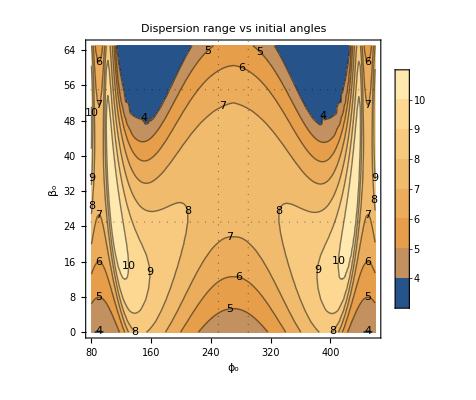

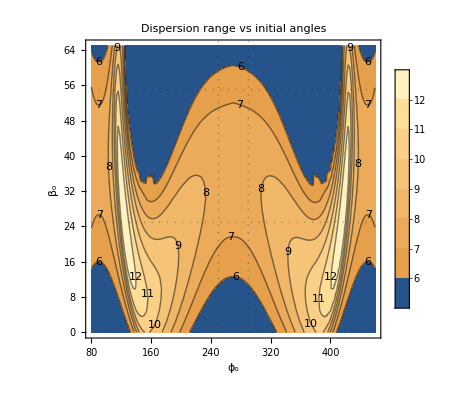

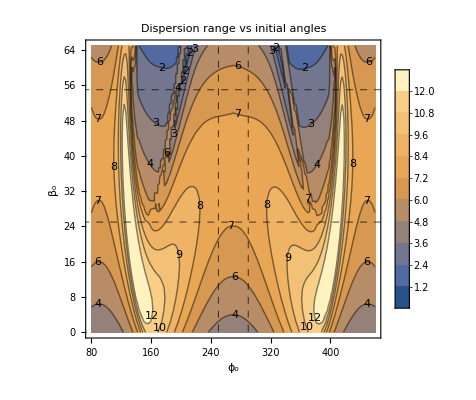

```mathematica
(* Contour plot the results of above sim block *)
dispList = {};
dispList2={};
dispList3={};
zdispList = {};
zdispList2={};
zdispList3={};
For[p=1, p<= Length[angles], p++,
For[b=1,b<=Length[anglesBeta],b++,
AppendTo[dispList,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta[[p,b,6]]}];
AppendTo[dispList2,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta2[[p,b,6]]}];
AppendTo[dispList3,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta3[[p,b,6]]}];
AppendTo[zdispList,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta[[p,b,7]]}];
AppendTo[zdispList2,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta2[[p,b,7]]}];
AppendTo[zdispList3,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta3[[p,b,7]]}];

]
]
(*Print[dispList]*)
contour = ListContourPlot[dispList,InterpolationOrder->1,Contours->Range[4,12,1], 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{250,290},{25,55}},
GridLinesStyle->Directive[Black,Thick,Dotted],
PlotLabel->"Dispersion range vs initial angles"];

contour2 = ListContourPlot[dispList2,InterpolationOrder->4,Contours->Range[6,12,1], 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{250,290},{25,55}},
GridLinesStyle->Directive[Black,Thick,Dotted],
PlotLabel->"Dispersion range vs initial angles"];

contour3 = ListContourPlot[dispList3,InterpolationOrder->1,Contours->10, 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{250,290},{25,55}},
GridLinesStyle->Directive[Black,Thick,Dashed],
PlotLabel->"Dispersion range vs initial angles"];

Show[contour]
Show[contour2]
Show[contour3]

(*(*Print[dispList]*)
zcontour = ListContourPlot[zdispList,InterpolationOrder->1,Contours->Range[0,5,.5], 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{265,275},{38,42}},
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Off-horiz range vs initial angles"];

zcontour2 = ListContourPlot[zdispList2,InterpolationOrder->1,Contours->Range[0,5,.5], 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{265,275},{38,42}},
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Off-horiz range vs initial angles"];

zcontour3 = ListContourPlot[zdispList3,InterpolationOrder->1,Contours->Range[0,5,.5], 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{265,275},{38,42}},
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Off-horiz range vs initial angles"];
Show[zcontour]
Show[zcontour2]
Show[zcontour3]*)
```

```mathematica
(* SPin rate contours *)
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[α, o]=(0.1)*((2*π)/360);
Subscript[ϕ, o]=270*((2*π)/360);
Subscript[v, o]=10;
Subscript[vx, o] = Subscript[v, o]*Cos[40*((2π)/360)];
Subscript[vy, o] = Subscript[v, o]*Sin[40*((2π)/360)];
Subscript[vz, o]=0; 
ω=1600;
resultsTableOmega = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[v, o]*Cos[30*((2π)/360)],Subscript[v, o]*Sin[30*((2π)/360)],Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles}, {omega,initialOmegas}];
resultsTableOmega2 = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[v, o]*Cos[40*((2π)/360)],Subscript[v, o]*Sin[40*((2π)/360)],Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles}, {omega,initialOmegas}];
resultsTableOmega3 = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[v, o]*Cos[50*((2π)/360)],Subscript[v, o]*Sin[50*((2π)/360)],Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles}, {omega,initialOmegas}];
```

Clear::ssym: x_o is not a symbol or a string.

Clear::ssym: y_o is not a symbol or a string.

Clear::ssym: z_o is not a symbol or a string.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

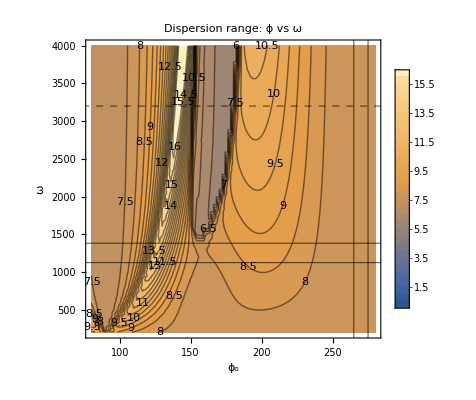

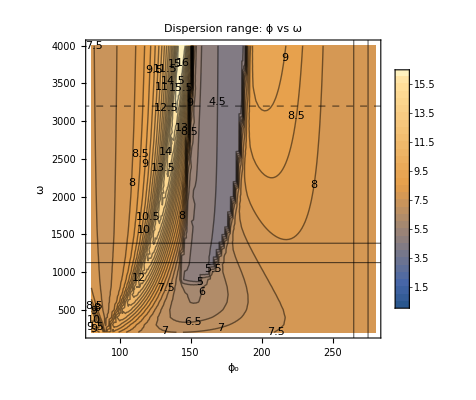

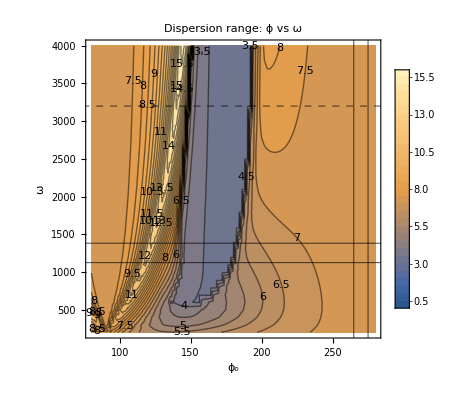

```mathematica
dispList = {};
dispList2 = {};
dispList3 = {};
zdispList = {};
For[p=1, p<= Length[angles], p++,
For[o=1,o<=Length[initialOmegas],o++,
AppendTo[dispList,{angles[[p]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTableOmega[[p,o,6]]}];
AppendTo[dispList2,{angles[[p]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTableOmega2[[p,o,6]]}];
AppendTo[dispList3,{angles[[p]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTableOmega3[[p,o,6]]}];


]
]
(*Print[dispList]*)
ListContourPlot[dispList,InterpolationOrder->1,Contours->Range[0,16,.5], 
ContourLabels->True,
PlotLegends->Automatic,
PlotRange->All,
FrameLabel->{"ϕ_o","ω"},
GridLines-> { {265,275},{1122,1382,{3200,Directive[Black,Dashed]}} },
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Dispersion range: ϕ vs ω"]

ListContourPlot[dispList2,InterpolationOrder->1,Contours->Range[0,16,.5], 
ContourLabels->True,
PlotLegends->Automatic,
PlotRange->All,
FrameLabel->{"ϕ_o","ω"},
GridLines-> { {265,275},{1122,1382,{3200,Directive[Black,Dashed]}} },
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Dispersion range: ϕ vs ω"]

ListContourPlot[dispList3,InterpolationOrder->1,Contours->Range[0,16,.5], 
ContourLabels->True,
PlotLegends->Automatic,
PlotRange->All,
FrameLabel->{"ϕ_o","ω"},
GridLines-> { {265,275},{1122,1382,{3200,Directive[Black,Dashed]}} },
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Dispersion range: ϕ vs ω"]
```

```mathematica
(* beta omega backspin*)
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[v, o]=9.81;
Subscript[α, o]=(0.1)*((2*π)/360);
Subscript[ϕ, o]=270*((2*π)/360);
Subscript[vx, o] = Subscript[v, o]*Cos[40*((2π)/360)];
Subscript[vy, o] = Subscript[v, o]*Sin[40*((2π)/360)];
Subscript[vz, o]=0; 
ω=1600;
resultsTableBetaOmega= Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],Subscript[ϕ, o],omega],{omega,initialOmegas}, {beta,anglesBeta}];
```

Clear::ssym: x_o is not a symbol or a string.

Clear::ssym: y_o is not a symbol or a string.

Clear::ssym: z_o is not a symbol or a string.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

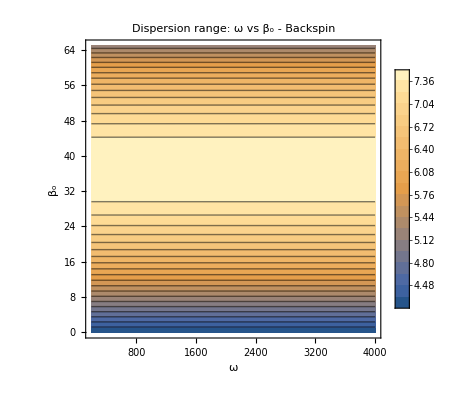

```mathematica
dispList = {};
zdispList = {};
For[o=1, o<= Length[initialOmegas], o++,
For[b=1,b<=Length[anglesBeta],b++,
AppendTo[dispList,{initialOmegas[[o]]/(2π),anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,6]]}];
AppendTo[zdispList,{initialOmegas[[o]]/(2π),anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,7]]}];

]
]
(*Print[dispList]*)
contour = ListContourPlot[dispList,InterpolationOrder->1,Contours->20, 
ContourLabels->Automatic,
PlotLegends->Automatic,
FrameLabel->{"ω","β_o"},
PlotLabel->"Dispersion range: ω vs β_o - Backspin"];

seedpoints = { {(√(5.51^2+4.63^2))/R,40.06},{(√(4.85^2+5.0^2))/R,45.89},{(√(3.23^2+3.15^2))/R,44.29},{(√(3.67^2+2.83^2))/R,37.61} }; (*from auditorium*)

Show[contour]
```

```mathematica
(* beta omega topspin*)
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[α, o]=(0)*((2*π)/360);
Subscript[ϕ, o]=91*((2*π)/360);
Subscript[vx, o] = Subscript[v, o]*Cos[40*((2π)/360)];
Subscript[vy, o] = Subscript[v, o]*Sin[40*((2π)/360)];
Subscript[vz, o]=0; 
Subscript[v, o]=10;
ω=1600;
resultsTableBetaOmega= Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],Subscript[ϕ, o],omega],{omega,initialOmegas}, {beta,anglesBeta}];
```

Clear::ssym: x_o is not a symbol or a string.

Clear::ssym: y_o is not a symbol or a string.

Clear::ssym: z_o is not a symbol or a string.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

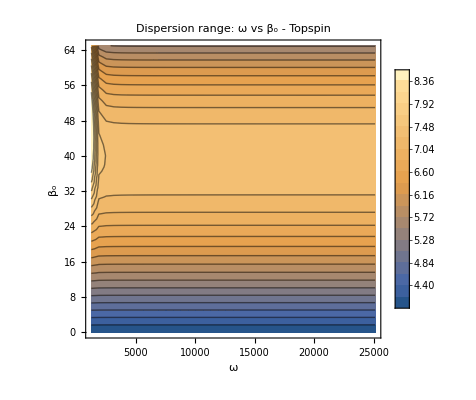

```mathematica
dispList = {};
zdispList = {};
For[o=1, o<= Length[initialOmegas], o++,
For[b=1,b<=Length[anglesBeta],b++,
AppendTo[dispList,{initialOmegas[[o]],anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,6]]}];
AppendTo[zdispList,{initialOmegas[[o]],anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,7]]}];

]
]
(*Print[dispList]*)
ListContourPlot[dispList,InterpolationOrder->1,Contours->20, 
ContourLabels->Automatic,
PlotLegends->Automatic,
FrameLabel->{"ω","β_o"},
PlotLabel->"Dispersion range: ω vs β_o - Topspin"]
```

```mathematica
(* beta omega sidespin*)
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[α, o]=(0.1)*((2*π)/360);
Subscript[ϕ, o]=180*((2*π)/360);
Subscript[vx, o] = Subscript[v, o]*Cos[45*((2π)/360)];
Subscript[vy, o] = Subscript[v, o]*Sin[45*((2π)/360)];
Subscript[vz, o]=0; 
Subscript[v, o]=10;
ω=1600;
resultsTableBetaOmega= Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],Subscript[ϕ, o],omega],{omega,initialOmegas}, {beta,anglesBeta}];
```

Clear::ssym: x_o is not a symbol or a string.

Clear::ssym: y_o is not a symbol or a string.

Clear::ssym: z_o is not a symbol or a string.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

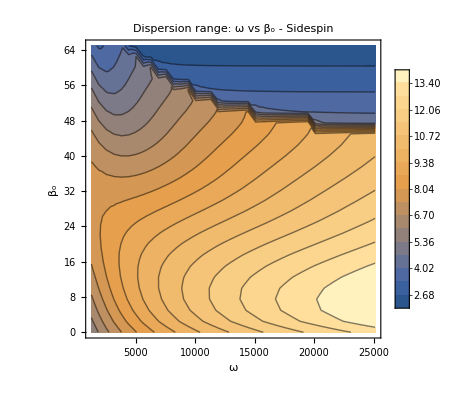

```mathematica
dispList = {};
zdispList = {};
For[o=1, o<= Length[initialOmegas], o++,
For[b=1,b<=Length[anglesBeta],b++,
AppendTo[dispList,{initialOmegas[[o]],anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,6]]}];
AppendTo[zdispList,{initialOmegas[[o]],anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,7]]}];

]
]
(*Print[dispList]*)
ListContourPlot[dispList,InterpolationOrder->1,Contours->20, 
ContourLabels->Automatic,
PlotLegends->Automatic,
FrameLabel->{"ω","β_o"},
PlotLabel->"Dispersion range: ω vs β_o - Sidespin"]
```

```mathematica
phiLow=90;
phiHi=270;
betaLow=0;
betaHi=65;
omegaLow=2;
omegaHi=10;
angles = Range[phiLow*((2*π)/360),phiHi*((2*π)/360),2.5*((2*π)/360)];
anglesBeta = Range[betaLow*((2*π)/360),betaHi*((2*π)/360),2*((2*π)/360)];
initialOmegas = 2π*Range[omegaLow,omegaHi,1];
```

```mathematica
(* 3d + color *)
$HistoryLength=10;
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[v, o] = 10;
Subscript[α, o]=(0.1)*((2*π)/360);
Subscript[ϕ, o]=180*((2*π)/360);
Subscript[vx, o] = Subscript[v, o]*Cos[45*((2π)/360)];
Subscript[vy, o] = Subscript[v, o]*Sin[45*((2π)/360)];
Subscript[vz, o]=0; 
Subscript[v, o]=10;
ω=1600;
Monitor[
resultsTablePhiBetaOmega1= Table[solveEquations[Subscript[x, o],1,Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi;*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]]
Monitor[
resultsTablePhiBetaOmega75= Table[solveEquations[Subscript[x, o],.75,Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi;*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]]
Monitor[
resultsTablePhiBetaOmega5= Table[solveEquations[Subscript[x, o],.5,Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]]
```

Clear::ssym: x_o is not a symbol or a string.

Clear::ssym: y_o is not a symbol or a string.

Clear::ssym: z_o is not a symbol or a string.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

{{{{90.,0.1,0,4 π,0.45947,4.53849,0.102627,-1},{90.,0.1,2,4 π,0.503331,4.96889,0.139837,-1},{90.,0.1,4,4 π,0.555718,5.47939,0.180771,-1},{90.,0.1,6,4 π,0.616049,6.0593,0.210899,-1},26,{90.,0.1,60,4 π,2.03118,8.66671,0.249874,-1},{90.,0.1,62,4 π,2.0597,8.17752,0.251486,-1},{90.,0.1,64,4 π,2.08633,7.66569,0.252233,-1}},7,{1}},{{1},8},70,{1}}
 |  |  |  |

{1}
 |  |  |  |

{{{{90.,0.1,0,4 π,0.320081,3.17084,0.0288282,-1},{90.,0.1,2,4 π,0.358285,3.54343,0.0421823,-1},{90.,0.1,4,4 π,0.401434,3.95862,0.0634976,-1},{90.,0.1,6,4 π,0.451063,4.43012,0.0973838,-1},26,{90.,0.1,60,4 π,1.97871,8.4649,0.250809,-1},{90.,0.1,62,4 π,2.00792,7.99371,0.25251,-1},{90.,0.1,64,4 π,2.03516,7.49912,0.253375,-1}},7,{1}},71,{{1},7,{1}}}
 |  |  |  |

```mathematica
(*1 - beta 
2 - omega
3 - phi 
4 - dep var (disp)*)

overallList1 = {};
overallList75 = {};
overallList5 = {};
dispList1 = {};
dispList5 = {};
dispList75 = {};
bestList1 = {};
bestList75 = {};
bestList5 = {};
worstList1 = {};
worstList75 = {};
worstList5 = {};
diffList1 = {};
diffList75 = {};
diffList5 = {};
For[b=1,b<=Length[anglesBeta],b++,
For[o=1, o<= Length[initialOmegas], o++,
maxrange1 = 0;
bestPhi1=0;
minrange1 = 1000;
worstPhi1=0;
maxrange75 = 0;
bestPhi75=0;
minrange75 = 1000;
worstPhi75=0;
maxrange5 = 0;
bestPhi5=0;
minrange5 = 1000;
worstPhi5=0;
For[p=1,p<=Length[angles],p++,

range1 = resultsTablePhiBetaOmega1[[p,o,b,6]];
If[range1>maxrange1,maxrange1=range1;bestPhi1=angles[[p]](360/(2π))];
If[range1<minrange1,minrange1=range1;worstPhi1=angles[[p]](360/(2π))];

range75 = resultsTablePhiBetaOmega75[[p,o,b,6]];
If[range75>maxrange75,maxrange75=range75;bestPhi75=angles[[p]](360/(2π))];
If[range1<minrange75,minrange75=range1;worstPhi75=angles[[p]](360/(2π))];

range5 = resultsTablePhiBetaOmega5[[p,o,b,6]];
If[range5>maxrange5,maxrange5=range5;bestPhi5=angles[[p]](360/(2π))];
If[range1<minrange5,minrange5=range1;worstPhi5=angles[[p]](360/(2π))];

AppendTo[dispList1,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTablePhiBetaOmega1[[p,o,b,1;;6]]}];
AppendTo[dispList75,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTablePhiBetaOmega75[[p,o,b,1;;6]]}];
AppendTo[dispList5,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTablePhiBetaOmega5[[p,o,b,1;;6]]}];

];
AppendTo[bestList1,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi1}];
AppendTo[bestList75,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi75}];
AppendTo[bestList5,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi5}];
AppendTo[worstList1,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),worstPhi1}];
AppendTo[worstList75,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),worstPhi75}];
AppendTo[worstList5,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),worstPhi5}];
AppendTo[diffList1,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi1-worstPhi1}];
AppendTo[diffList75,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi75-worstPhi75}];
AppendTo[diffList5,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi5-worstPhi5}];
];
];
dispList;
```

```mathematica
(*  saved calculation results*)
Save["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\SimData\\bm_bestPhi_v2",{bestList1,bestList75,bestList5,worstList1,worstList75,worstList5,diffList1,diffList5,diffList75,dispList1,dispList75,dispList5}]
```

```mathematica
(* Load calculation results from file *)
Get["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\SimData\\sd_bestPhi_v2"]
```

{{90.,0,200,{90.,0.1,0,400 π,0.318781,2.87951}},{92.5,0,200,{92.5,0.1,0,400 π,0.319325,2.88346}},{95.,0,200,{95.,0.1,0,400 π,0.321767,2.90308}},{97.5,0,200,{97.5,0.1,0,400 π,0.32621,2.9397}},93944,{265.,64,4000,{265.,0.1,64,8000 π,1.70019,5.29343}},{267.5,64,4000,{267.5,0.1,64,8000 π,1.69668,5.30503}},{270.,64,4000,{270.,0.1,64,8000 π,1.69581,5.31601}}}
 |  |  |  |

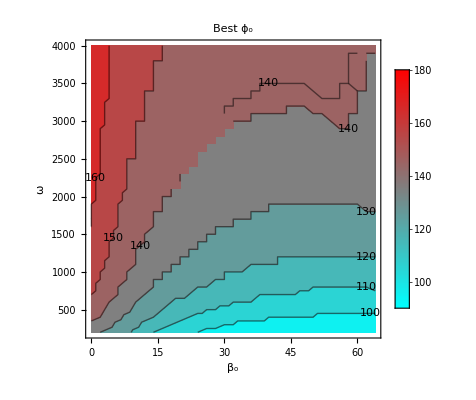

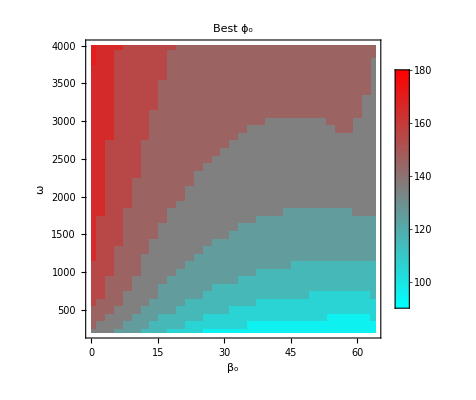

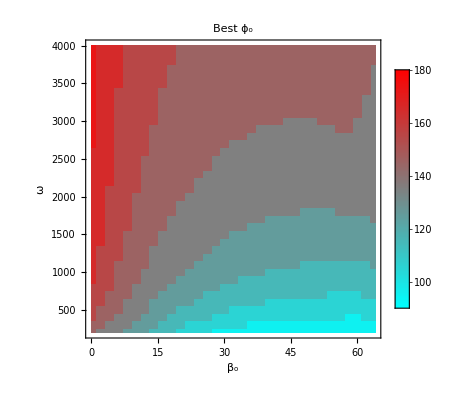

```mathematica
plotBP1=ListContourPlot[bestList1,InterpolationOrder->1, Contours->Range[90,180,10],
ColorFunction->(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),
ColorFunctionScaling->False,
PlotLegends->BarLegend[{(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),{90,180}}],
FrameLabel->{"β_o", "ω"},
ContourLabels->All,
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Best ϕ_o"]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\functional\\seed\\sd_TEMP1.jpg",plotBP1];

plotBP75=ListContourPlot[bestList75,InterpolationOrder->0, Contours->Range[90,180,10],
ColorFunction->(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),
ColorFunctionScaling->False,
PlotLegends->BarLegend[{(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),{90,180}}],
FrameLabel->{"β_o", "ω"},
ContourLabels->All,
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Best ϕ_o"]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\functional\\seed\\sd_TEMP75.jpg",plotBP75];

plotBP5=ListContourPlot[bestList5,InterpolationOrder->0, Contours->Range[90,180,10],
ColorFunction->(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),
ColorFunctionScaling->False,
PlotLegends->BarLegend[{(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),{90,180}}],
FrameLabel->{"β_o", "ω"},
ContourLabels->All,
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Best ϕ_o"]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\functional\\seed\\sd_TEMP5.jpg",plotBP5];
```

```mathematica
(*ListContourPlot3D[dispList,Contours->25,ColorFunction->"TemperatureMap",AxesLabel->{"ϕ","β","ω"},
ViewPoint->{0,0,Infinity}]*)
ListSliceContourPlot3D[dispList,
{"ZStackedPlanes",3},
AxesLabel->{"ϕ_o","β_o","ω"}]
```

-Graphics3D-